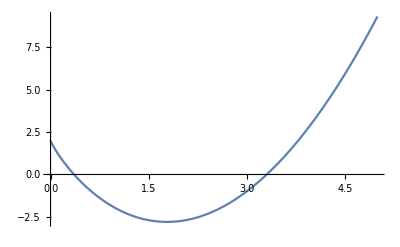

```mathematica
f[x_]=x Log[3,x]+x^2-5 x+2;
Plot[f[x],{x,0,5}]
```

```mathematica
g[x_]=(x Log[3,x]+x^2+2)/5;
```

```mathematica
N[g'[1]]
```

0.582048

```mathematica
epsilon=0.001;
```

```mathematica
x0=1;
x1=g[x0];
i=1;

While[Abs[x1-x0]>epsilon,
x0=x1;
x1=g[x1];
i++;];
Round[x1, epsilon]
i
```

0.359

6